This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 1: General Concepts and Simple Examples ch1Introduction.nb

## Test Cases

### testCase0002: 15-degree with 1,2,3,4,5-cycle at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
```

### testCase0006 (1-z^2)+w^2

```mathematica
$theFunction=(1-z^2)+w^2;
```

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3


aForm[$theFunction]
aForm[$theFunction]//TeXForm
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

\left(1+4 z^2\right)+\left(\frac{5}{2}+\frac{3}{4} z\right) w^2+\left(z-\frac{3}{4} z^2\right) w^3

### Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-0.406393-0.724149 ⅈ,0.812786+1.4483 ⅈ,0.812786+1.4483 ⅈ}

{-1.95584-5.02162 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ}

### testCase0023: Function with three 4-cycle branches at the origin and in a_2

#### Expansion at the origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 
aForm[$theFunction]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

### Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-0.406393-0.724149 ⅈ,0.812786+1.4483 ⅈ,0.812786+1.4483 ⅈ}

{-1.95584-5.02162 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ}

### testCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;


aForm[$theFunction]
aForm[$theFunction]//TeXForm
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

\left(-z^2+1 z^3\right)+\left(-4 z+3 z^2\right) w+\left(-z^3-9 z^4\right) w^2+\left(-2+8 z+4 z^2-4 z^3\right) w^3+\left(6-8
   z^2+7 z^3+8 z^4\right) w^4

### Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-0.406393-0.724149 ⅈ,0.812786+1.4483 ⅈ,0.812786+1.4483 ⅈ}

{-1.95584-5.02162 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ,-4.44089×10^-16-8.88178×10^-16 ⅈ}

## Section 1: Study of z^{1/2}

### Section 1.1: Compute singular points

```mathematica
(*
 compute the singular points of z^{1/2}
*)
 $theFunction=z-w^2;
res=Resultant[$theFunction,D[$theFunction,w],w]
(*
 Compute the zeros of the resultant
*)
SolveValues[res==0,z]
```

4 z

{0}

### Section 1.2: Create annular diagram

```mathematica
singularPointsG={Blue,PointSize[0.025],Point[{0,0}]};
annular1=Circle[{0,0},4];
annular1G={Opacity[0.3],Brown,Disk[{0,0},4]}
Show[Graphics@{singularPointsG,annular1G},Axes->True]
```

{Opacity[0.3],RGBColor[0.6, 0.4, 0.2],Disk[{0,0},4]}

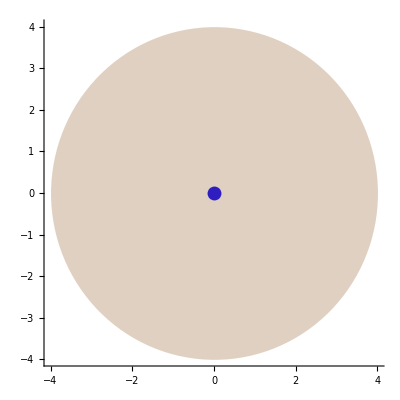

-Graphics-

### Section 1.3: Creating plots of branch sheets

#### Create imaginary sheets

```mathematica
f1[z_]:=z^(1/2);
imag1= ParametricPlot3D[{Re@z,Im@z,Im[f1[z]]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Blue}];
imag2= ParametricPlot3D[{Re@z,Im@z,-Im[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Red}];
 Show[{imag1,imag2},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

#### Create real sheets

```mathematica
real1= ParametricPlot3D[{Re@z,Im@z,Re[f1[z]]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Blue}];
real2= ParametricPlot3D[{Re@z,Im@z,-Re[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Red}];

 Show[{real1,real2},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Section 1.4: Creating a default contour over the branch sheets

Notice in the following code how a contour over the default definition of z^{1/2} starting at z=Exp[Pi i/4] on the blue sheet and encounters the default branch-cut at the negative real axis and abruptly drops down to the lower blue sheet of the branch rather than analytically-continuing onto the red sheet.

```mathematica
(* create contour with arrowhead *)
startZ=3/2Exp[Pi I/4];
startZG=Graphics3D@{PointSize[0.025],Green,Point@{Re@startZ,Im@startZ,Im@Sqrt[startZ]}};
arrowPts=Table[{Re@z,Im@z,Im@Sqrt[z]}/.z->3/2Exp[I t],{t,7Pi/4,7Pi/4+0.1,0.01}];
arrow3D=Graphics3D@{Arrowheads[0.04],Arrow[BezierCurve[arrowPts]]};
(* create default branch surfaces of z^{1/2}*)
imagContour=ParametricPlot3D[{Re@z,Im@z,Im[z^(1/2)]}/.z->3/2Exp[I t],{t,Pi/4+0.05,7 Pi/4},PlotStyle->{Thickness[0.005],Black}];

Show[{imag1,imag2,imagContour,startZG,arrow3D},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

Illustration of the real sheets of z^{1/2}

```mathematica
real1= ParametricPlot3D[{Re@z,Im@z,Re[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Blue}];
real2= ParametricPlot3D[{Re@z,Im@z,-Re[z^{1/2}]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.3],Red}];
Show[{real1,real2},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

The same branch-cut discontinuity is observed over the real sheets (note the kink at the negative real axis:

```mathematica
realContour=ParametricPlot3D[{Re@z,Im@z,Re[z^(1/2)]}/.z->Exp[I t],{t,0,2 Pi},PlotStyle->Yellow];
Show[{real1,real2,realContour},PlotRange->All,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted]]
```

-Graphics3D-

### Section 1.5: Creating analytically-continuous contour over z^{1/2}

#### Section 1.5.1: Create contour over real surface

```mathematica
theFunction=-z+w^2;
(*
 start the contour at (1/2 Sqrt[1/2])
*)
z0=3/2 Exp[-Pi/2 I];
w0=-Sqrt[z0];
(*
 revolve around the branch sheets 4 Pi
*)
tStart=-Pi/2;
tEnd=tStart+4  Pi;
(*
 create z(t)
*)
Z[t_]:=3/2 Exp[I t];
(*
 solve IVP
*)
wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[Z[t],t])/. {w->w[t],z->Z[t]});
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd}];

mPlot=ParametricPlot3D[{Re@z,Im@z,Re@theSol[t]}/. z->Z[t],{t,tStart+0.05,tEnd-0.05},PlotStyle->{Thickness[0.005],Black}];

startZ2=Z[tStart];
startZG2=Graphics3D@{PointSize[0.025],Green,Point@{Re@startZ2,Im@startZ2,-Re@Sqrt[startZ2]}};
arrowPts2=Table[{Re@z,Im@z,-Re@Sqrt[z]}/.z->3/2Exp[I t],{t,tEnd-1,tEnd-0.05,0.01}];
arrow3D2=Graphics3D@{Arrowheads[0.04],Arrow[BezierCurve[arrowPts2]]};





Show[{real1,real2,mPlot,arrow3D2,startZG2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],PlotRange->All,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

#### Section 1.5.2: Create contour over imag surfaace

```mathematica
theFunction=-z+w^2;
(*
 start the contour at (1/2 Sqrt[1/2])
*)
z0=3/2 Exp[-Pi/2 I];
w0=-Sqrt[z0];
(*
 revolve around the branch sheets 4 Pi
*)
tStart=-Pi/2;
tEnd=tStart+4  Pi;
(*
 create z(t)
*)
Z[t_]:=3/2 Exp[I t];
(*
 solve IVP
*)
wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[Z[t],t])/. {w->w[t],z->Z[t]});
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd}];

mPlot=ParametricPlot3D[{Re@z,Im@z,Im@theSol[t]}/. z->Z[t],{t,tStart+0.05,tEnd-0.05},PlotStyle->{Thickness[0.005],Black}];

startZ2=Z[tStart];
startZG2=Graphics3D@{PointSize[0.025],Green,Point@{Re@startZ2,Im@startZ2,-Im@Sqrt[startZ2]}};
arrowPts2=Table[{Re@z,Im@z,-Im@Sqrt[z]}/.z->3/2Exp[I t],{t,tEnd-1,tEnd-0.05,0.01}];
arrow3D2=Graphics3D@{Arrowheads[0.04],Arrow[BezierCurve[arrowPts2]]};





Show[{imag1,imag2,mPlot,arrow3D2,startZG2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],PlotRange->All,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Section 1.6: Interactive 3D plot of mIVP contour analytically-continuing across branch surfaces

```mathematica
tStart=-Pi/2;
tEnd=tStart+4Pi;

gPoint3D=Graphics3D@{PointSize[0.02],Green,Point@{Re@Z[tStart],Im@Z[tStart],Re@theSol[tStart]}};
 Manipulate[
ppReal=ParametricPlot3D[{Re@z,Im@z,Re@theSol[t]}/. z->Z[t],{t,tStart,tStop},PlotStyle->{Thickness[0.01],Black}];
arrowArray=Table[{Re@z,Im@z,Re@theSol[t]}/.z->Z[t],{t,tStart+0.05,tStop+0.05,(tStop+0.06-tStart)/50}];
arrowG=Graphics3D@{Thickness[0.005],Arrow@arrowArray};
Show[{real1,real2,arrowG,gPoint3D},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["Re[z]",14,Bold,Black],Style["Im[z]",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],PlotRange->All,BoxRatios->{1, 1, 1}],
{{tStop,1.596},tStart+0.001,tEnd+0.06,Appearance->"Labeled"}
]
```

ParametricPlot3D::plln: Limiting value tStart in {t,tStart,1.596} is not a machine-sized real number.

Table::iterb: Iterator {t,0.05+tStart,1.646,1/50 (1.656-tStart)} does not have appropriate bounds.

Show::gcomb: Could not combine the graphics objects in Show[{real1,real2,,gPoint3D},AxesEdge→{{-1,-1},{1,-1},{-1,-1}},FaceGrids→{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel→{Re[z],Im[z],Re(w)},FaceGridsStyle→Directive[color,Dashing[{0,Small}]],PlotRange→All,BoxRatios→{1,1,1}].

## Section 2: Study of (1-z^2)-w^2=0

```mathematica
$theFunction=(1-z^2)-w^2;
theF[z_]:=Sqrt[1-z^2];
theSheets=SolveValues[$theFunction==0,w]
p1=ParametricPlot3D[{Re@z,Im@z,Re@theSheets[[1]]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.25],Blue},BoxRatios->{1, 1, 1},PlotRange->2.2]
p2=ParametricPlot3D[{Re@z,Im@z,Re@theSheets[[2]]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.25],Red},BoxRatios->{1, 1, 1},PlotRange->2.2]
Show[{p1,p2},PlotRange->2.2,ImageSize->300,ViewPoint->{1.8027796685821182,-2.233730535848765,1.7917682215520347}]
```

{-√(1-z^2),√(1-z^2)}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
c1=ParametricPlot3D[{Re@z,Im@z,Re@theF[z]}/.z->3/2 Exp[I t],{t,Pi/4+0.05,9Pi/4-0.05},PlotStyle->Black];
theZ[t_]:=3/2 Exp[I t];
startZ2=Z[Pi/4];
tStart=Pi/4;
tEnd=tStart+2 Pi;
startZG2=Graphics3D@{PointSize[0.025],Green,Point@{Re@startZ2,Im@startZ2,Re@Sqrt[1-startZ2^2]}};
arrowPts2=Table[{Re@z,Im@z,Re@Sqrt[1-z^2]}/.z->3/2Exp[I t],{t,tStart+0.2,tStart+Pi/4,0.01}];
arrow3D2=Graphics3D@{Thick,Arrowheads[0.04],Arrow[BezierCurve[arrowPts2]]};

Show[{p1,p2},PlotRange->All]


Show[{p1,p2,c1,startZG2,arrow3D2},PlotRange->2.2,ImageSize->300,ViewPoint->{1.8027796685821182,-2.233730535848765,1.7917682215520347}]
```

-Graphics3D-

-Graphics3D-

```mathematica
theFunction=(1-z^2)-w^2;
(*
 start the contour at (1/2 Sqrt[1/2])
*)
z0=3/2 Exp[Pi/4 I];
w0=Sqrt[1-z0^2];
(*
 revolve around the branch sheets 4 Pi
*)
tStart=Pi/4;
tEnd=tStart+2  Pi;
(*
 create z(t)
*)
Z[t_]:=3/2 Exp[I t];
(*
 solve IVP
*)
wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[Z[t],t])/. {w->w[t],z->Z[t]});
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd}];

mPlot=ParametricPlot3D[{Re@z,Im@z,Re@theSol[t]}/. z->Z[t],{t,tStart+0.05,tEnd-0.05},PlotStyle->{Thickness[0.005],Blue}];

startZ2=Z[tStart];
startZG2=Graphics3D@{PointSize[0.025],Green,Point@{Re@startZ2,Im@startZ2,Re@Sqrt[1-startZ2^2]}};
arrowPts2=Table[{Re@z,Im@z,Re@Sqrt[1-z^2]}/.z->3/2Exp[I t],{t,tStart+1,tStart+1.5,0.01}];
arrow3D2=Graphics3D@{Thick,Arrowheads[0.04],Arrow[BezierCurve[arrowPts2]]};





Show[{p1,p2,mPlot,arrow3D2,startZG2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1, 1},PlotRange->2.2,ImageSize->300,ViewPoint->{1.8027796685821182,-2.233730535848765,1.7917682215520347}]
```

-Graphics3D-

```mathematica
theFunction=(1-z^2)-w^2;
(*
 create z(t)
*)
Z[t_]:=-1+2/3 Exp[I t];
(*
 solve IVP
*)
(*
 start the contour at (1/2 Sqrt[1/2])
*)
tStart=Pi/4;
tEnd=tStart+4Pi;
z0=Z[tStart];
w0=Sqrt[1-z0^2];

wDeriv2=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[Z[t],t])/. {w->w[t],z->Z[t]});
theSol2=NDSolveValue[{wDeriv2,w[tStart]==w0},w,{t,tStart,tEnd}];

mPlot2=ParametricPlot3D[{Re@z,Im@z,Re@theSol2[t]}/. z->Z[t],{t,tStart+0.1,tEnd-0.1},PlotStyle->{Thickness[0.005],Red}];

startZ3=Z[tStart];
startZG3=Graphics3D@{PointSize[0.025],Blue,Point@{Re@startZ3,Im@startZ3,Re@Sqrt[1-startZ3^2]}};

arrowPts3=Table[{Re@z,Im@z,Re@theSol2[t]}/.z->-1+2/3Exp[I t],{t,Pi+1,Pi+2,0.01}];
arrow3D3=Graphics3D@{Thick,Red,Arrowheads[0.04],Arrow[BezierCurve[arrowPts3]]};
```

```mathematica
Show[{p1,p2,mPlot2,mPlot,arrow3D2,startZG2,mPlot2,startZG3,arrow3D3},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["x",14,Bold,Black],Style["y",14,Bold,Black],Style["Re(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1, 1},PlotRange->2.2,ImageSize->300,ViewPoint->{1.8027796685821182,-2.233730535848765,1.7917682215520347}]
```

-Graphics3D-

```mathematica
theFunction=(1-z^2)+w^2;

theF[z_]:=Sqrt[z^2-1];
theSheets=SolveValues[theFunction==0,w]
p1=ParametricPlot3D[{Re@z,Im@z,Im@theSheets[[1]]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.25],Blue},BoxRatios->{1, 1, 1},PlotRange->2.2];
p2=ParametricPlot3D[{Re@z,Im@z,Im@theSheets[[2]]}/.z->r Exp[I t],{r,0,2},{t,-Pi,Pi},PlotStyle->{Opacity[0.25],Red},BoxRatios->{1, 1, 1},PlotRange->2.2];
 Show[{p1},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["Re(z)",14,Bold,Black],Style["Im(z)",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1, 1},PlotRange->2.2,ImageSize->300,ViewPoint->{1.8027796685821182,-2.233730535848765,1.7917682215520347}]

 Show[{p1,p2},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},FaceGrids->{{{0,0,-1},{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1}}}},AxesLabel->{Style["Re(z)",14,Bold,Black],Style["Im(z)",14,Bold,Black],Style["Im(w)",14,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1, 1},PlotRange->2.2,ImageSize->300,ViewPoint->{1.8027796685821182,-2.233730535848765,1.7917682215520347}]
```

{-√(-1+z^2),√(-1+z^2)}

-Graphics3D-

-Graphics3D-

## Section 3: Study of absolute and relative coordinates

### Section 3.1: Absolute and relative study of (1-z^2)-w^2

```mathematica
(*
 define function
*)
theFunction=(1-z^2)-w^2;
(* aSeries is in terms of absolute coordinate z *)
aSeries=w/.AsymptoticSolve[theFunction==0,w,{z,1,100}];
aSeries[[All,1;;5]]//N
zTest=1+3/2 Exp[Pi I/6];
zTest=5/2;
Print["aSeries vals: ",Sort[aSeries/.z->zTest//N]]
wVals=NSolveValues[theFunction==0/.z->zTest,w];
Print["Roots: ",wVals//N];
(* now simulate a relative power expansion computed by Newton polygons and Laurent's theorem *)
pSeries=aSeries/.(-1+z)->z;
pSeries[[1,1;;5]]//N
zr=zTest-1;
Print["pSeries vals: ",Sort[pSeries/.z->zr//N]]
```

{(0.-1.41421 ⅈ) √(-1.+z)-(0.+0.353553 ⅈ) (-1.+z)^(3/2)+(0.+0.0441942 ⅈ) (-1.+z)^(5/2)-(0.+0.0110485 ⅈ) (-1.+z)^(7/2)+(0.+0.00345267 ⅈ) (-1.+z)^(9/2),(0.+1.41421 ⅈ) √(-1.+z)+(0.+0.353553 ⅈ) (-1.+z)^(3/2)-(0.+0.0441942 ⅈ) (-1.+z)^(5/2)+(0.+0.0110485 ⅈ) (-1.+z)^(7/2)-(0.+0.00345267 ⅈ) (-1.+z)^(9/2)}

aSeries vals: {0.-2.29129 ⅈ,0.+2.29129 ⅈ}

Roots: {0.-2.29129 ⅈ,0.+2.29129 ⅈ}

(0.-1.41421 ⅈ) √z-(0.+0.353553 ⅈ) z^(3/2)+(0.+0.0441942 ⅈ) z^(5/2)-(0.+0.0110485 ⅈ) z^(7/2)+(0.+0.00345267 ⅈ) z^(9/2)

pSeries vals: {0.-2.29129 ⅈ,0.+2.29129 ⅈ}

### Section 9.2: Absolute and relative study of testCase0017

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
aSeries=w/.AsymptoticSolve[$theFunction==0,w,{z,1/2 I,25}]; 
aSeries[[All,1;;5]]//MatrixForm
 zTest=1/2 I+1/3 Exp[Pi I/6];
aSeries/.z->zTest//N
pSeries=aSeries/.(-I/2+z)->z;
pSeries[[All,1;;4]]
wVals=NSolveValues[$theFunction==0/.z->zTest,w]
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

((-168/73+(302 ⅈ)/73)-(9837651068/891440449+(1193583600 ⅈ)/891440449) (-ⅈ/2+z)-(6693328964890403952/4452307182360938833+(96441205822498130296 ⅈ)/4452307182360938833) (-ⅈ/2+z)^2+(887757510257370057031474548720/22237087478294135877816190561+(3785296807196275133214372096 ⅈ)/22237087478294135877816190561) (-ⅈ/2+z)^3-(43719982406527168016056310226136812672/111063329474740357761148998462266676337-(8879837231188667207326182295217006494944 ⅈ)/111063329474740357761148998462266676337) (-ⅈ/2+z)^4
-4 √(-6/409-(40 ⅈ)/409) √(-ⅈ/2+z)-(22144/167281-(17064 ⅈ)/167281) (-ⅈ/2+z)+(29055540/68417929+(126037822 ⅈ)/68417929) √(-6/409-(40 ⅈ)/409) (-ⅈ/2+z)^(3/2)+(5311089570792/11445019581049+(3399434302720 ⅈ)/11445019581049) (-ⅈ/2+z)^2-(6767608733757909/4681013008649041-(7764060992781660 ⅈ)/4681013008649041) √(-3/818-(10 ⅈ)/409) (-ⅈ/2+z)^(5/2)
4 √(-6/409-(40 ⅈ)/409) √(-ⅈ/2+z)-(22144/167281-(17064 ⅈ)/167281) (-ⅈ/2+z)-(29055540/68417929+(126037822 ⅈ)/68417929) √(-6/409-(40 ⅈ)/409) (-ⅈ/2+z)^(3/2)+(5311089570792/11445019581049+(3399434302720 ⅈ)/11445019581049) (-ⅈ/2+z)^2+(6767608733757909/4681013008649041-(7764060992781660 ⅈ)/4681013008649041) √(-3/818-(10 ⅈ)/409) (-ⅈ/2+z)^(5/2))

{-3.68129+1.50428 ⅈ,-0.600176+0.596205 ⅈ,0.533184-0.461916 ⅈ}

{(-168/73+(302 ⅈ)/73)-(9837651068/891440449+(1193583600 ⅈ)/891440449) z-(6693328964890403952/4452307182360938833+(96441205822498130296 ⅈ)/4452307182360938833) z^2+(887757510257370057031474548720/22237087478294135877816190561+(3785296807196275133214372096 ⅈ)/22237087478294135877816190561) z^3,-4 √(-6/409-(40 ⅈ)/409) √z-(22144/167281-(17064 ⅈ)/167281) z+(29055540/68417929+(126037822 ⅈ)/68417929) √(-6/409-(40 ⅈ)/409) z^(3/2)+(5311089570792/11445019581049+(3399434302720 ⅈ)/11445019581049) z^2,4 √(-6/409-(40 ⅈ)/409) √z-(22144/167281-(17064 ⅈ)/167281) z-(29055540/68417929+(126037822 ⅈ)/68417929) √(-6/409-(40 ⅈ)/409) z^(3/2)+(5311089570792/11445019581049+(3399434302720 ⅈ)/11445019581049) z^2}

{-3.6812+1.50427 ⅈ,-0.600176+0.596205 ⅈ,0.533184-0.461916 ⅈ}

## Section 4: Set up root test for f(z,w)=(1-z^2)+w^2

{0.0820307,Null}

-1.41421 √(-1.+z)-0.353553 (-1.+z)^(3/2)+0.0441942 (-1.+z)^(5/2)
1.41421 √(-1.+z)+0.353553 (-1.+z)^(3/2)-0.0441942 (-1.+z)^(5/2)

-1.41421 √z-0.353553 z^(3/2)+0.0441942 z^(5/2)-0.0110485 z^(7/2)+0.00345267 z^(9/2)

LCM: 2

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199}

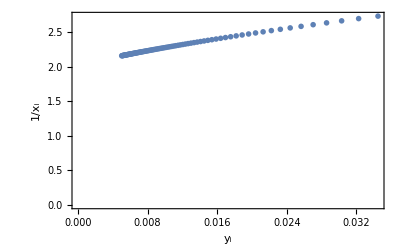

```mathematica
functionA=(1-z^2)+w^2;
(* generate series via AsymptoticSolve *)
AbsoluteTiming[aSeries=w/.AsymptoticSolve[functionA==0,w,{z,1,100}];]
Style[aSeries[[All,1;;3]]//N//TableForm,10]
(* convert aSeries to pSeries *)
pSeries=aSeries/.(-1+z)->z;
pSeries[[1,1;;5]]//N
(* create root test points  *)
 testSeries=pSeries[[1]]; 
expList=Exponent[testSeries,z,List];
coefList=Coefficient[testSeries,z,#]&/@ expList;
theLCM=LCM@@(Denominator@expList);
Print["LCM: ",theLCM];
 numerators=theLCM expList
rootTestTable=Table[
{1/numerators[[k]],N[1/(Abs[coefList[[k]]]^(theLCM/numerators[[k]])),25]},
{k,15,Length@coefList}];
(* plot root test points *)
lp1=ListPlot[rootTestTable,PlotStyle->{PointSize[0.01]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style[,16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},FrameTicksStyle->Directive[Black,12,Black,Bold]]
```

Estimated radius of convergence: 2.05322

2.05322+20.4025 x

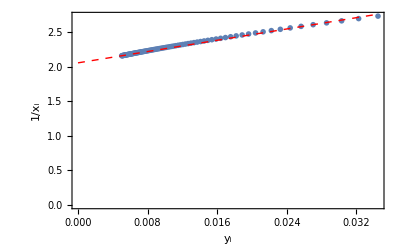

```mathematica
(* use NMinimize to construct lim inf curve and estimate R *)
 dataVals=rootTestTable[[5;;]];
plotXStart=rootTestTable[[-1,1]];
plotXEnd=rootTestTable[[1,1]];
endTerms=Length@rootTestTable;
linearLine=c0+c1 x/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1},WorkingPrecision->MachinePrecision][[2]];
Print["Estimated radius of convergence: ",linearLine/.x->0]
linearLine

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
Show[{lp1,linearPlot}]
```

## Section 5: Study of testCase0023, creating monodromy reference table

### Section 5.1: Compute power expansions at the origin

```mathematica
(*  define function *)
theConst=2/3+ⅈ/4;
function23=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 
pSeries=w/.AsymptoticSolve[function23==0,w,{z,0,30}];
```

```mathematica
(* finding which pSeries corresponds to which root of f(z,w) *)
 zTest=1/3 Exp[Pi I/6];
pResults=pSeries/.z->zTest//N
wVals=NSolveValues[function23==0/.z->zTest,w]
rootIndex=1;
difTable=Abs[#-wVals[[rootIndex]]&/@ pResults];
pos=Position[difTable,Min@difTable][[1,1]];
Print["Root index ",rootIndex," is associated with expansion ",pos]
```

{-0.847645-0.414158 ⅈ,-0.909916-0.110106 ⅈ,-0.406369-0.440236 ⅈ,-0.468614-0.0597909 ⅈ,0.468614+0.0597909 ⅈ,0.406369+0.440236 ⅈ,0.909916+0.110106 ⅈ,0.847645+0.414158 ⅈ,-2.95291-0.0155088 ⅈ,0.842405+2.24375 ⅈ,-0.842405-2.24375 ⅈ,2.95291+0.0155088 ⅈ}

{-2.95291-0.0155088 ⅈ,-0.909916-0.110106 ⅈ,-0.847645-0.414158 ⅈ,-0.842405-2.24375 ⅈ,-0.468614-0.0597909 ⅈ,-0.406369-0.440236 ⅈ,0.406369+0.440236 ⅈ,0.468614+0.0597909 ⅈ,0.842405+2.24375 ⅈ,0.847645+0.414158 ⅈ,0.909916+0.110106 ⅈ,2.95291+0.0155088 ⅈ}

Root index 1 is associated with expansion 9

```mathematica
pSeries[[1,1;;5]]//N
```

(-0.666667-0.25 ⅈ)-(0.2799+0.244276 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z+(0.012384+0.0906903 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z

### Section 5.2: Conjugate a series manually and identify it in the list of AsymptoticSolve series

```mathematica
theConst=2/3+ⅈ/4;
tempF=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 
pSeries2=w/.AsymptoticSolve[tempF==0,w,{z,0,2}];
expList=Exponent[pSeries2[[1]],z,List]
coefList=Coefficient[pSeries2[[1]],z,#]&/@expList;
theN=2;
conjSeries=Plus @@MapThread[#1 z^#2 Exp[2 theN Pi I #2]&,{coefList,expList}]//N;
Style[conjSeries,10]
```

{0,1/4,1/2,3/4,1,5/4,3/2,7/4,2}

(-0.666667-0.25 ⅈ)+(0.2799+0.244276 ⅈ) z^(1/4)+(0.0176408+0.032719 ⅈ) √z-(0.012384+0.0906903 ⅈ) z^(3/4)+(0.00770177-0.0339537 ⅈ) z-(0.0213216-0.0324143 ⅈ) z^(5/4)-(0.0242145-0.0176625 ⅈ) z^(3/2)+(0.0162017-0.00450886 ⅈ) z^(7/4)+(0.0246405+0.00215767 ⅈ) z^2

### Section 5.3: Set up data for Root Test for 120 terms of aSeries and display results

The Root Test data is set up in the following code and note how the lim Sup of points are tending to 1 as the points become closer to the y-axis.  This limiting case is the radius of convergence of the series.  Note in this case since expansion center is the origin, pSeries=aSeries.

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120}

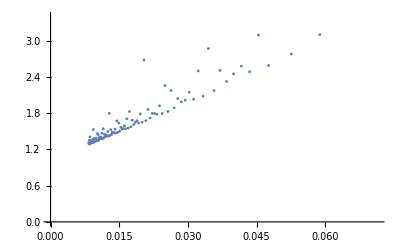

```mathematica
testSeries=pSeries[[1]]; 
expList=Exponent[testSeries,z,List];
coefList=Coefficient[testSeries,z,#]&/@ expList;
theLCM=LCM@@(Denominator@expList);
 numerators=theLCM expList
rootTestTable=Table[
{1/numerators[[k]],N[1/(Abs[coefList[[k]]]^(4/numerators[[k]])),25]},
{k,15,Length@coefList}];
lp1=ListPlot[rootTestTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}]
```

Estimated radius of convergence: 1.01597

1.01597+31.767 x

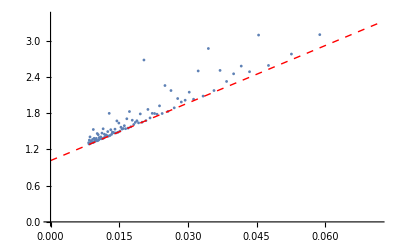

```mathematica
(* use NMinimize to construct lim inf curve and estimate R *)
 dataVals=rootTestTable[[5;;]];
plotXStart=rootTestTable[[-1,1]];
plotXEnd=rootTestTable[[1,1]];
endTerms=Length@rootTestTable;
linearLine=c0+c1 x/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1},WorkingPrecision->MachinePrecision][[2]];
Print["Estimated radius of convergence: ",linearLine/.x->0]
linearLine

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
Show[{lp1,linearPlot}]
```

### Section 5.4: Create monodromy reference table manually for testCase0002

```mathematica
function2=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
AbsoluteTiming[pSeries=w/.AsymptoticSolve[function2==0,w,{z,I,10}];]
Style[pSeries[[All,1;;3]]//N//TableForm,10]
```

{146.468,Null}

((0.-1. ⅈ)+z)^(1/9)+(0.333333+0.333333 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.+0.0555556 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-0.939693-0.34202 ⅈ) ((0.-1. ⅈ)+z)^(1/9)-(0.455342-0.122008 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.0357104+0.042558 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(0.766044+0.642788 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.122008-0.455342 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.0547115+0.00964712 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-0.5-0.866025 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.333333+0.333333 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.0481125-0.0277778 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(0.173648+0.984808 ⅈ) ((0.-1. ⅈ)+z)^(1/9)-(0.455342-0.122008 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.0190011-0.0522051 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(0.173648-0.984808 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.122008-0.455342 ⅈ) ((0.-1. ⅈ)+z)^(2/3)-(0.0190011+0.0522051 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-0.5+0.866025 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.333333+0.333333 ⅈ) ((0.-1. ⅈ)+z)^(2/3)-(0.0481125+0.0277778 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(0.766044-0.642788 ⅈ) ((0.-1. ⅈ)+z)^(1/9)-(0.455342-0.122008 ⅈ) ((0.-1. ⅈ)+z)^(2/3)-(0.0547115-0.00964712 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-0.939693+0.34202 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.122008-0.455342 ⅈ) ((0.-1. ⅈ)+z)^(2/3)-(0.0357104-0.042558 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-6.+0.000257202 ⅈ)+(0.0552983+12. ⅈ) ((0.-1. ⅈ)+z)+(30.001+0.0311223 ⅈ) ((0.-1. ⅈ)+z)^2
(-0.782277-0.262915 ⅈ)+(0.991586+0.714729 ⅈ) ((0.-1. ⅈ)+z)+(19.9687-25.0672 ⅈ) ((0.-1. ⅈ)+z)^2
(-0.462763+0.670325 ⅈ)-(0.373807+0.14683 ⅈ) ((0.-1. ⅈ)+z)-(27.996-23.3522 ⅈ) ((0.-1. ⅈ)+z)^2
(0.0211654-0.800492 ⅈ)-(2.22942-1.44271 ⅈ) ((0.-1. ⅈ)+z)-(26.5094-15.6251 ⅈ) ((0.-1. ⅈ)+z)^2
(0.476546+0.629857 ⅈ)+(1.48809+0.853642 ⅈ) ((0.-1. ⅈ)+z)+(24.0542-30.7049 ⅈ) ((0.-1. ⅈ)+z)^2
(0.747329-0.237032 ⅈ)+(0.0682568-2.86427 ⅈ) ((0.-1. ⅈ)+z)+(6.73151+24.2636 ⅈ) ((0.-1. ⅈ)+z)^2

```mathematica
zTest=5/1000 Exp[Pi I/6];
pResults=pSeries/.z->zTest//N
wVals=NSolveValues[function2==0/.z->zTest,w]
difTable=Abs[#-wVals[[1]]&/@ pResults];
pos=Position[difTable,Min@difTable][[1,1]]
```

```mathematica
aSeries=pSeries[[1]]/.(-I+z)->z;
aSeries[[1;;5]]//N
```

z^(1/9)+(0.333333+0.333333 ⅈ) z^(2/3)+(0.+0.0555556 ⅈ) z^(7/9)-(0.+2.61111 ⅈ) z^(10/9)-(1.-1.22222 ⅈ) z^(11/9)

```mathematica
testSeries=aSeries; 
expList=Exponent[testSeries,z,List]
```

{1/9,2/3,7/9,10/9,11/9,4/3,13/9,5/3,16/9,17/9,2,19/9,20/9,7/3,22/9,23/9,8/3,25/9,26/9,3,28/9,29/9,10/3,31/9,32/9,11/3,34/9,35/9,4,37/9,38/9,13/3,40/9,41/9,14/3,43/9,44/9,5,46/9,47/9,16/3,49/9,50/9,17/3,52/9,53/9,6,55/9,56/9,19/3,58/9,59/9,20/3,61/9,62/9,7,64/9,65/9,22/3,67/9,68/9,23/3,70/9,71/9,8,73/9,74/9,25/3,76/9,77/9,26/3,79/9,80/9,9,82/9,83/9,28/3,85/9,86/9,29/3,88/9,89/9,10}

z^(1/9)+(0.333333+0.333333 ⅈ) z^(2/3)+(0.+0.0555556 ⅈ) z^(7/9)-(0.+2.61111 ⅈ) z^(10/9)-(1.-1.22222 ⅈ) z^(11/9)

{1/9,2/3,7/9,10/9,11/9,4/3,13/9,5/3,16/9,17/9,2,19/9,20/9,7/3,22/9,23/9,8/3,25/9,26/9,3,28/9,29/9,10/3,31/9,32/9,11/3,34/9,35/9,4,37/9,38/9,13/3,40/9,41/9,14/3,43/9,44/9,5,46/9,47/9,16/3,49/9,50/9,17/3,52/9,53/9,6,55/9,56/9,19/3,58/9,59/9,20/3,61/9,62/9,7,64/9,65/9,22/3,67/9,68/9,23/3,70/9,71/9,8,73/9,74/9,25/3,76/9,77/9,26/3,79/9,80/9,9,82/9,83/9,28/3,85/9,86/9,29/3,88/9,89/9,10}

{1,6,7,10,11,12,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90}

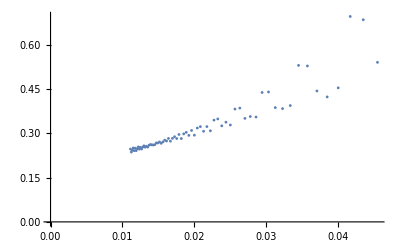

```mathematica
testSeries=aSeries; 
testSeries[[1;;5]]//N
expList=Exponent[testSeries,z,List]
coefList=Coefficient[testSeries,z,#]&/@ expList;
theLCM=LCM@@(Denominator@expList);
 numerators=theLCM expList
rootTestTable=Table[
{1/numerators[[k]],N[1/(Abs[coefList[[k]]]^(4/numerators[[k]])),25]},
{k,15,Length@coefList}];
lp1=ListPlot[rootTestTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}]
```

## Section 6: Study of testCase0002

### Section 6.1: Compute expansion at the origin using AsymptoticSolve for testCase0002

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
```

```mathematica
AbsoluteTiming[pSeries=w/.AsymptoticSolve[$theFunction==0,w,{z,0,25}];]
Style[pSeries[[All,1;;6]]//N//TableForm,10]
```

{2.31152,Null}

-3.-0.0555556 z+1.50206 z^2-0.0834667 z^3-0.742788 z^4-0.0264546 z^5
(0.-0.408248 ⅈ) √z+0.0277778 z+(0.+0.0047251 ⅈ) z^(3/2)-0.00102881 z^2-(0.+0.204377 ⅈ) z^(5/2)-2.95827 z^3
(0.+0.408248 ⅈ) √z+0.0277778 z-(0.+0.0047251 ⅈ) z^(3/2)-0.00102881 z^2+(0.+0.204377 ⅈ) z^(5/2)-2.95827 z^3
-1. z^(4/3)+2. z^3+0.333333 z^(10/3)-0.666667 z^(13/3)-16. z^(14/3)-4.33333 z^5
(0.5+0.866025 ⅈ) z^(4/3)+2. z^3-(0.166667+0.288675 ⅈ) z^(10/3)+(0.333333+0.57735 ⅈ) z^(13/3)+(8.-13.8564 ⅈ) z^(14/3)-4.33333 z^5
(0.5-0.866025 ⅈ) z^(4/3)+2. z^3-(0.166667-0.288675 ⅈ) z^(10/3)+(0.333333-0.57735 ⅈ) z^(13/3)+(8.+13.8564 ⅈ) z^(14/3)-4.33333 z^5
(-0.707107-0.707107 ⅈ) z^(9/4)+0.25 z^5+(0.176777+0.176777 ⅈ) z^(25/4)-(0.243068-0.243068 ⅈ) z^(31/4)-(0.176777+0.176777 ⅈ) z^(33/4)+(0.+1.5 ⅈ) z^(17/2)
(0.707107+0.707107 ⅈ) z^(9/4)+0.25 z^5-(0.176777+0.176777 ⅈ) z^(25/4)+(0.243068-0.243068 ⅈ) z^(31/4)+(0.176777+0.176777 ⅈ) z^(33/4)+(0.+1.5 ⅈ) z^(17/2)
(0.707107-0.707107 ⅈ) z^(9/4)+0.25 z^5-(0.176777-0.176777 ⅈ) z^(25/4)+(0.243068+0.243068 ⅈ) z^(31/4)+(0.176777-0.176777 ⅈ) z^(33/4)-(0.+1.5 ⅈ) z^(17/2)
(-0.707107+0.707107 ⅈ) z^(9/4)+0.25 z^5+(0.176777-0.176777 ⅈ) z^(25/4)-(0.243068+0.243068 ⅈ) z^(31/4)-(0.176777-0.176777 ⅈ) z^(33/4)-(0.+1.5 ⅈ) z^(17/2)
-1. z^(16/5)-0.2 z^(26/5)+0.2 z^7+0.08 z^(36/5)+0.2 z^9+0.152 z^(46/5)
(0.809017+0.587785 ⅈ) z^(16/5)+(0.161803+0.117557 ⅈ) z^(26/5)+0.2 z^7-(0.0647214+0.0470228 ⅈ) z^(36/5)+0.2 z^9-(0.122971+0.0893434 ⅈ) z^(46/5)
(-0.309017-0.951057 ⅈ) z^(16/5)-(0.0618034+0.190211 ⅈ) z^(26/5)+0.2 z^7+(0.0247214+0.0760845 ⅈ) z^(36/5)+0.2 z^9+(0.0469706+0.144561 ⅈ) z^(46/5)
(-0.309017+0.951057 ⅈ) z^(16/5)-(0.0618034-0.190211 ⅈ) z^(26/5)+0.2 z^7+(0.0247214-0.0760845 ⅈ) z^(36/5)+0.2 z^9+(0.0469706-0.144561 ⅈ) z^(46/5)
(0.809017-0.587785 ⅈ) z^(16/5)+(0.161803-0.117557 ⅈ) z^(26/5)+0.2 z^7-(0.0647214-0.0470228 ⅈ) z^(36/5)+0.2 z^9-(0.122971-0.0893434 ⅈ) z^(46/5)

```mathematica
Style[MapThread[{#1,#2}&,{Range@Length@pSeries,pSeries[[All,1;;5]]//N}]//MatrixForm,10]
```

(1 | -3.-0.0555556 z+1.50206 z^2-0.0834667 z^3-0.742788 z^4
2 | (0.-0.408248 ⅈ) √z+0.0277778 z+(0.+0.0047251 ⅈ) z^(3/2)-0.00102881 z^2-(0.+0.204377 ⅈ) z^(5/2)
3 | (0.+0.408248 ⅈ) √z+0.0277778 z-(0.+0.0047251 ⅈ) z^(3/2)-0.00102881 z^2+(0.+0.204377 ⅈ) z^(5/2)
4 | -1. z^(4/3)+2. z^3+0.333333 z^(10/3)-0.666667 z^(13/3)-16. z^(14/3)
5 | (0.5+0.866025 ⅈ) z^(4/3)+2. z^3-(0.166667+0.288675 ⅈ) z^(10/3)+(0.333333+0.57735 ⅈ) z^(13/3)+(8.-13.8564 ⅈ) z^(14/3)
6 | (0.5-0.866025 ⅈ) z^(4/3)+2. z^3-(0.166667-0.288675 ⅈ) z^(10/3)+(0.333333-0.57735 ⅈ) z^(13/3)+(8.+13.8564 ⅈ) z^(14/3)
7 | (-0.707107-0.707107 ⅈ) z^(9/4)+0.25 z^5+(0.176777+0.176777 ⅈ) z^(25/4)-(0.243068-0.243068 ⅈ) z^(31/4)-(0.176777+0.176777 ⅈ) z^(33/4)
8 | (0.707107+0.707107 ⅈ) z^(9/4)+0.25 z^5-(0.176777+0.176777 ⅈ) z^(25/4)+(0.243068-0.243068 ⅈ) z^(31/4)+(0.176777+0.176777 ⅈ) z^(33/4)
9 | (0.707107-0.707107 ⅈ) z^(9/4)+0.25 z^5-(0.176777-0.176777 ⅈ) z^(25/4)+(0.243068+0.243068 ⅈ) z^(31/4)+(0.176777-0.176777 ⅈ) z^(33/4)
10 | (-0.707107+0.707107 ⅈ) z^(9/4)+0.25 z^5+(0.176777-0.176777 ⅈ) z^(25/4)-(0.243068+0.243068 ⅈ) z^(31/4)-(0.176777-0.176777 ⅈ) z^(33/4)
11 | -1. z^(16/5)-0.2 z^(26/5)+0.2 z^7+0.08 z^(36/5)+0.2 z^9
12 | (0.809017+0.587785 ⅈ) z^(16/5)+(0.161803+0.117557 ⅈ) z^(26/5)+0.2 z^7-(0.0647214+0.0470228 ⅈ) z^(36/5)+0.2 z^9
13 | (-0.309017-0.951057 ⅈ) z^(16/5)-(0.0618034+0.190211 ⅈ) z^(26/5)+0.2 z^7+(0.0247214+0.0760845 ⅈ) z^(36/5)+0.2 z^9
14 | (-0.309017+0.951057 ⅈ) z^(16/5)-(0.0618034-0.190211 ⅈ) z^(26/5)+0.2 z^7+(0.0247214-0.0760845 ⅈ) z^(36/5)+0.2 z^9
15 | (0.809017-0.587785 ⅈ) z^(16/5)+(0.161803-0.117557 ⅈ) z^(26/5)+0.2 z^7-(0.0647214-0.0470228 ⅈ) z^(36/5)+0.2 z^9)

### Section 6.2: Choose a series index of the pSeries expansions and determine its cycle size

```mathematica
(*
 determine the cycle size as the smallest number divisible by all denominators of powers of z 
*)
pIndex=2;
cycleF[z_]= pSeries[[pIndex]];
eList=Exponent[cycleF[z],z,List]
theCycleSize=LCM@@(Denominator@eList)
```

{1/2,1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10,21/2,11,23/2,12,25/2,13,27/2,14,29/2,15,31/2,16,33/2,17,35/2,18,37/2,19,39/2,20,41/2,21,43/2,22,45/2,23,47/2,24,49/2,25}

2

### Section 6.3: Construct the monodromy reference table entry for the selected series generator

```mathematica
(*
 construct the monodromy reference table entry for the selected power expansion relating the Puiseux series index of the series to the mrp root
*)
mrpPoint=1/20 Exp[Pi I/6];
testVal=cycleF[mrpPoint];
wVals=NSolveValues[$theFunction==0/.z->mrpPoint,w]
difTable=Abs[#-testVal]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]]
difTable[[pos]]//N

(* format is {cycle size,{Puiseux series index, root index}} *)

mrpEntry={cycleSize,{pIndex,pos}}
```

{-3.00053+0.0018487 ⅈ,-0.0224953+0.0884885 ⅈ,-0.0141019-0.0115859 ⅈ,-0.00318196+0.0183984 ⅈ,-0.00109226-0.000452359 ⅈ,-0.000452466+0.00109223 ⅈ,-0.0000627278-0.0000279608 ⅈ,-0.0000459762+0.0000510172 ⅈ,7.20813×10^-6-0.000068298 ⅈ,0.0000343128+0.000059491 ⅈ,0.0000671825-0.0000142498 ⅈ,0.000452331-0.00109215 ⅈ,0.00109212+0.000452437 ⅈ,0.017287-0.00606434 ⅈ,0.0248955-0.087842 ⅈ}

15

1.09604×10^-17

{2,{2,15}}

### Section 6.4: Use root test to estimate radius of convergence of series

This section uses the root test to estimate the radius of convergence of the 1-cycle series of testCase0002 at the origin.  Since AsymptoticSolve uses exact arithmetic, the process takes times to create even a  small number of terms giving a rough estimate of R.  In Chapter 3, a numeric method is used to generate a larger number of terms quickly and to obtain a more precise estimate.

LCM: 1

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

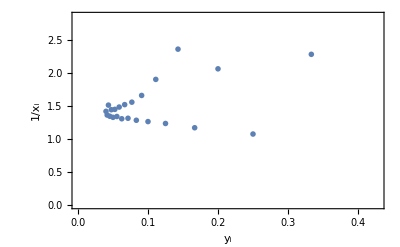

```mathematica
(* create root test points  *)
 testSeries=pSeries[[1]]; 
expList=Exponent[testSeries,z,List];
coefList=Coefficient[testSeries,z,#]&/@ expList;
theLCM=LCM@@(Denominator@expList);
Print["LCM: ",theLCM];
 numerators=theLCM expList
rootTestTable=Table[
{1/numerators[[k]],N[1/(Abs[coefList[[k]]]^(theLCM/numerators[[k]])),25]},
{k,2,Length@coefList}];
(* plot root test points *)
lp1=ListPlot[rootTestTable,PlotStyle->{PointSize[0.01]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style[,16,Bold,Black],-Pi/2]},AxesOrigin->{0,0},FrameTicksStyle->Directive[Black,12,Black,Bold]]
```

Estimated radius of convergence: 1.39104

1.39104-1.31034 x

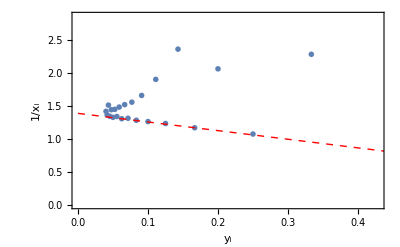

```mathematica
(* use NMinimize to construct lim inf curve and estimate R *)
 dataVals=rootTestTable[[5;;]];
plotXStart=rootTestTable[[-1,1]];
plotXEnd=rootTestTable[[1,1]];
endTerms=Length@rootTestTable;
linearLine=c0+c1 x/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1},WorkingPrecision->MachinePrecision][[2]];
Print["Estimated radius of convergence: ",linearLine/.x->0]
linearLine

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
Show[{lp1,linearPlot}]
```

### Section 6.5: Create a branch plot of the 5-cycle branch by manually conjugating a generator series

```mathematica
(*
 generate branch sheet plot of 5-cycle branch, distance to nearest singular point is about 0.16 so set plot range at 0.1
*)
(* choose series 12 as the generator for the 5-cycle branch *)

 pIndex=12;
cycleF[z_]= pSeries[[pIndex]];
cycleF[z]//N

 p1=ParametricPlot3D[{Re@z,Im@z,Re@cycleF[z]}/.z->r Exp[I t],{r,0,1/10},{t,-Pi,Pi},BoxRatios->{1, 1, 1}]
```

(0.809017+0.587785 ⅈ) z^(16/5)+(0.161803+0.117557 ⅈ) z^(26/5)+0.2 z^7-(0.0647214+0.0470228 ⅈ) z^(36/5)+0.2 z^9-(0.122971+0.0893434 ⅈ) z^(46/5)+(0.226525-0.16458 ⅈ) z^(54/5)+0.2 z^11-(0.0595437+0.043261 ⅈ) z^(56/5)-(0.0618034-0.190211 ⅈ) z^(63/5)+(0.407745-0.296244 ⅈ) z^(64/5)-0.2 z^13+(0.0336033+0.0244142 ⅈ) z^(66/5)+(0.00988854-0.0304338 ⅈ) z^(73/5)+(0.616147-0.447657 ⅈ) z^(74/5)-0.4 z^15+(0.0727882+0.0528837 ⅈ) z^(76/5)+(0.210132+0.646718 ⅈ) z^(82/5)+(0.31495-0.969317 ⅈ) z^(83/5)-(0.0561781-0.0408158 ⅈ) z^(84/5)-0.4 z^17+(0.038547+0.028006 ⅈ) z^(86/5)-1.2 z^18+(0.322861+0.993664 ⅈ) z^(92/5)+(1.00151-3.08234 ⅈ) z^(93/5)-(0.993447-0.721781 ⅈ) z^(94/5)+0.2 z^19-(0.0235383+0.0171016 ⅈ) z^(96/5)-2.4 z^20+(1.76689+1.28372 ⅈ) z^(101/5)-(0.263925+0.812278 ⅈ) z^(102/5)+(0.866592-2.6671 ⅈ) z^(103/5)-(1.9568-1.4217 ⅈ) z^(104/5)+0.6 z^21-(0.376747+0.273723 ⅈ) z^(106/5)-(3.68912-2.6803 ⅈ) z^(109/5)-1.6 z^22+(4.85441+3.52694 ⅈ) z^(111/5)-(2.97406+9.15321 ⅈ) z^(112/5)-(0.581055-1.7883 ⅈ) z^(113/5)-(0.821248-0.596671 ⅈ) z^(114/5)+0.6 z^23-(0.902855+0.655963 ⅈ) z^(116/5)-(10.3295-7.50484 ⅈ) z^(119/5)+8.6 z^24+(4.62785+3.36233 ⅈ) z^(121/5)-(5.41964+16.6799 ⅈ) z^(122/5)-(3.52932-10.8621 ⅈ) z^(123/5)+(1.59169-1.15643 ⅈ) z^(124/5)-1.8 z^25

-Graphics3D-

### Section 6.6: Manually conjugate generator series for the 5-cycle branch and plot the sheets

```mathematica
(*
 manually conjugate the generator series for the 5-cycle branch
*)

 $reim=Re;
theSeries=pSeries[[pIndex]];
expList=Exponent[theSeries,z,List];
coefList=Coefficient[theSeries,z,#]&/@ expList;
conj1=Plus@@MapThread[#1 z^#2 Exp[2 Pi I #2]&,{coefList,expList}];
conjSet[j_]:=Plus@@MapThread[#1 z^#2 Exp[2 Pi I j #2]&,{coefList,expList}];
```

```mathematica
(*
 plot the full set of conjugate series
*)
theColors={Red,Blue,Green,Yellow,Purple,Orange};
conjPlots=Table[ParametricPlot3D[{Re@z,Im@z,Re@conjSet[j]}/.z->r Exp[I t],{r,0,1/10},{t,-Pi,Pi},BoxRatios->{1, 1, 1},PlotStyle->{Opacity[0.3],Blue}],
{j,0,4}];
Show[conjPlots]
```

### Section 6.7: Create a contour around the 5-cycle branch and overlay over branch sheets

```mathematica
(*
 create contour around 5-cycle branch of testCase0002 at the origin
*)
Z[t_]:=1/20 Exp[I t];
(*
 solve IVP
*)
(*
 start the contour at (1/2 Sqrt[1/2])
*)
tStart=Pi/6;
tEnd=tStart+10Pi;
z0=Z[tStart];
(*
 start contour on pSeries[[12]]
*)
w0=pSeries[[12]]/.z->z0;

wDeriv=w'[t]==((-(D[case0002F,z]/D[case0002F,w]) D[Z[t],t])/. {w->w[t],z->Z[t]});
theSol=NDSolveValue[{wDeriv,w[tStart]==w0},w,{t,tStart,tEnd}];

mPlot=ParametricPlot3D[{Re@z,Im@z,Re@theSol[t]}/. z->Z[t],{t,tStart+0.1,tEnd-0.1},PlotStyle->{Thickness[0.005],Yellow},BoxRatios->{1, 1, 1}]

Show[{conjPlots,mPlot}]
```

-Graphics3D-

-Graphics3D-

### Section 6.8: Study of power expansion at z=i for testCase0002

```mathematica
(*
 compute power expansions at z=i
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
AbsoluteTiming[pSeries2=w/.AsymptoticSolve[$theFunction==0,w,{z,I,10}];]
Style[pSeries2[[All,1;;3]]//N//TableForm,10]
```

{143.725,Null}

((0.-1. ⅈ)+z)^(1/9)+(0.333333+0.333333 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.+0.0555556 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-0.939693-0.34202 ⅈ) ((0.-1. ⅈ)+z)^(1/9)-(0.455342-0.122008 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.0357104+0.042558 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(0.766044+0.642788 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.122008-0.455342 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.0547115+0.00964712 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-0.5-0.866025 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.333333+0.333333 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.0481125-0.0277778 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(0.173648+0.984808 ⅈ) ((0.-1. ⅈ)+z)^(1/9)-(0.455342-0.122008 ⅈ) ((0.-1. ⅈ)+z)^(2/3)+(0.0190011-0.0522051 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(0.173648-0.984808 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.122008-0.455342 ⅈ) ((0.-1. ⅈ)+z)^(2/3)-(0.0190011+0.0522051 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-0.5+0.866025 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.333333+0.333333 ⅈ) ((0.-1. ⅈ)+z)^(2/3)-(0.0481125+0.0277778 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(0.766044-0.642788 ⅈ) ((0.-1. ⅈ)+z)^(1/9)-(0.455342-0.122008 ⅈ) ((0.-1. ⅈ)+z)^(2/3)-(0.0547115-0.00964712 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-0.939693+0.34202 ⅈ) ((0.-1. ⅈ)+z)^(1/9)+(0.122008-0.455342 ⅈ) ((0.-1. ⅈ)+z)^(2/3)-(0.0357104-0.042558 ⅈ) ((0.-1. ⅈ)+z)^(7/9)
(-6.+0.000257202 ⅈ)+(0.0552983+12. ⅈ) ((0.-1. ⅈ)+z)+(30.001+0.0311223 ⅈ) ((0.-1. ⅈ)+z)^2
(-0.782277-0.262915 ⅈ)+(0.991586+0.714729 ⅈ) ((0.-1. ⅈ)+z)+(19.9687-25.0672 ⅈ) ((0.-1. ⅈ)+z)^2
(-0.462763+0.670325 ⅈ)-(0.373807+0.14683 ⅈ) ((0.-1. ⅈ)+z)-(27.996-23.3522 ⅈ) ((0.-1. ⅈ)+z)^2
(0.0211654-0.800492 ⅈ)-(2.22942-1.44271 ⅈ) ((0.-1. ⅈ)+z)-(26.5094-15.6251 ⅈ) ((0.-1. ⅈ)+z)^2
(0.476546+0.629857 ⅈ)+(1.48809+0.853642 ⅈ) ((0.-1. ⅈ)+z)+(24.0542-30.7049 ⅈ) ((0.-1. ⅈ)+z)^2
(0.747329-0.237032 ⅈ)+(0.0682568-2.86427 ⅈ) ((0.-1. ⅈ)+z)+(6.73151+24.2636 ⅈ) ((0.-1. ⅈ)+z)^2

```mathematica
(*
 code to create monodromy reference table at z=I
*)
aSeries2=pSeries2/.(-I+z)->z;
Style[aSeries2[[All,1;;3]]//N//TableForm,10]

 zm=5/1000 Exp[Pi I/6];
mrp=aSeries2/.z->zm;
mrp//N
wVals=NSolveValues[case0002F==0/.z->I+zm,w]
difTable=Abs[wVals[[7]]-#]&/@ wVals
```

z^(1/9)+(0.333333+0.333333 ⅈ) z^(2/3)+(0.+0.0555556 ⅈ) z^(7/9)
(-0.939693-0.34202 ⅈ) z^(1/9)-(0.455342-0.122008 ⅈ) z^(2/3)+(0.0357104+0.042558 ⅈ) z^(7/9)
(0.766044+0.642788 ⅈ) z^(1/9)+(0.122008-0.455342 ⅈ) z^(2/3)+(0.0547115+0.00964712 ⅈ) z^(7/9)
(-0.5-0.866025 ⅈ) z^(1/9)+(0.333333+0.333333 ⅈ) z^(2/3)+(0.0481125-0.0277778 ⅈ) z^(7/9)
(0.173648+0.984808 ⅈ) z^(1/9)-(0.455342-0.122008 ⅈ) z^(2/3)+(0.0190011-0.0522051 ⅈ) z^(7/9)
(0.173648-0.984808 ⅈ) z^(1/9)+(0.122008-0.455342 ⅈ) z^(2/3)-(0.0190011+0.0522051 ⅈ) z^(7/9)
(-0.5+0.866025 ⅈ) z^(1/9)+(0.333333+0.333333 ⅈ) z^(2/3)-(0.0481125+0.0277778 ⅈ) z^(7/9)
(0.766044-0.642788 ⅈ) z^(1/9)-(0.455342-0.122008 ⅈ) z^(2/3)-(0.0547115-0.00964712 ⅈ) z^(7/9)
(-0.939693+0.34202 ⅈ) z^(1/9)+(0.122008-0.455342 ⅈ) z^(2/3)-(0.0357104-0.042558 ⅈ) z^(7/9)
(-6.+0.000257202 ⅈ)+(0.0552983+12. ⅈ) z+(30.001+0.0311223 ⅈ) z^2
(-0.782277-0.262915 ⅈ)+(0.991586+0.714729 ⅈ) z+(19.9687-25.0672 ⅈ) z^2
(-0.462763+0.670325 ⅈ)-(0.373807+0.14683 ⅈ) z-(27.996-23.3522 ⅈ) z^2
(0.0211654-0.800492 ⅈ)-(2.22942-1.44271 ⅈ) z-(26.5094-15.6251 ⅈ) z^2
(0.476546+0.629857 ⅈ)+(1.48809+0.853642 ⅈ) z+(24.0542-30.7049 ⅈ) z^2
(0.747329-0.237032 ⅈ)+(0.0682568-2.86427 ⅈ) z+(6.73151+24.2636 ⅈ) z^2

{0.561203+0.0396283 ⅈ,-0.532155-0.216656 ⅈ,0.417744+0.365225 ⅈ,-0.249318-0.485817 ⅈ,0.0595347+0.551719 ⅈ,0.134052-0.556981 ⅈ,-0.293869+0.484172 ⅈ,0.430231-0.337474 ⅈ,-0.527247+0.156374 ⅈ,-6.02938+0.0530069 ⅈ,-0.778853-0.257196 ⅈ,-0.464999+0.668529 ⅈ,0.00728274-0.800304 ⅈ,0.481771+0.637276 ⅈ,0.754384-0.248888 ⅈ}

{-6.02938+0.0530069 ⅈ,-0.778853-0.257196 ⅈ,-0.532155-0.216656 ⅈ,-0.527247+0.156374 ⅈ,-0.464999+0.668529 ⅈ,-0.293869+0.484172 ⅈ,-0.249318-0.485817 ⅈ,0.00728274-0.800304 ⅈ,0.0595347+0.551719 ⅈ,0.134052-0.556981 ⅈ,0.417744+0.365225 ⅈ,0.430231-0.337474 ⅈ,0.481771+0.637276 ⅈ,0.561203+0.0396283 ⅈ,0.754384-0.248888 ⅈ}

{5.80512,0.57678,0.390441,0.699753,1.17432,0.971011,0.,0.40589,1.08253,0.389919,1.08132,0.695552,1.34009,0.965939,1.03129}

## Section 7: Checking f_w(s_i,w_i)=0 for each singular point and some w_i with f(s_i,w_i)=0 for testCase0002

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
```

```mathematica
res= Resultant[$theFunction,D[$theFunction,w],w];
singList=DeleteDuplicates@NSolveValues[res==0,z,WorkingPrecision->25];
wVals=NSolveValues[$theFunction==0/.z->singList[[2]],w,WorkingPrecision->20]
D[$theFunction,w]/.{z->singList[[2]],w->#}&/@ wVals
```

{-1.668266600780184135+0.163724195599222736 ⅈ,-1.539984674-0.7411900269 ⅈ,-1.539984674-0.7411900269 ⅈ,-1.3177710592849707649+0.7385012338897737142 ⅈ,-0.9183804854773029188+1.1749908639433668841 ⅈ,-0.8670139349048434766-1.2510819073497047328 ⅈ,-0.3423795346043524031+1.462729597300429997 ⅈ,-0.1535776171068780195-1.4774727942880484991 ⅈ,0.3191633943236638197+1.35791639296702753 ⅈ,0.4121568085731471092-1.3506402409145386605 ⅈ,0.8590039289137389636+1.1329751373665733649 ⅈ,0.9897464732817337879-1.061876745278113446 ⅈ,1.2907481366020473803+0.6563313562301301819 ⅈ,1.3629354620944552659-0.5234852381717921824 ⅈ,1.4004119190871132156+0.0278713408575628665 ⅈ}

{-17744.208570113333-12900.337163319873 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-7548.349219852919-10020.240064483024 ⅈ,920.9752854701558-13768.707556502172 ⅈ,-10386.672067903642+9858.9939013718194 ⅈ,7213.8569499671091-17432.5870526532558 ⅈ,-11731.4942140912366+11096.045534673021 ⅈ,7943.34079524304206-10488.3497407135939 ⅈ,-1282.0939527332379+12616.4069713537634 ⅈ,14779.4881987965746-3939.5640946354997 ⅈ,5025.5016928893152+16346.8752978952214 ⅈ,18049.3459774363373+30.7738955244203 ⅈ,7687.7252698279756+14779.1641235350503 ⅈ,12241.0708260254778+4611.16300941825034 ⅈ}

## Section 8: Study of testCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

### Section 8.1: Create power expansion at z=0 using AsymptoticSolve (note aSeries=pSeries at origin)

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
Print[Style[aForm[$theFunction],10]]
aSeries=w/.AsymptoticSolve[$theFunction==0,w,{z,0,25}];
Style[MapThread[{#1,#2}&,{Range@Length@aSeries,aSeries[[All,1;;5]]//N}]//MatrixForm,10]
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

(1 | -0.25 z+0.0703125 z^2+0.020752 z^3+0.0039978 z^4-0.106094 z^5
2 | (0.-1.41421 ⅈ) √z-2.875 z+(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2-(0.+611.292 ⅈ) z^(5/2)
3 | (0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)
4 | 0.333333+4.66667 z-168.222 z^2+9523.5 z^3-658181. z^4)

### Section 8.2: Compute $theSingularList

```mathematica
res=Resultant[$theFunction,D[$theFunction,w],w]
```

-12288 z^3-1306656 z^4+3196480 z^5+4175488 z^6-19252432 z^7+12003992 z^8+29410688 z^9-60176968 z^10+30810996 z^11+51884752 z^12-116906556 z^13+78934466 z^14+51708792 z^15-161406268 z^16+125566475 z^17+51834520 z^18-171956148 z^19+78698668 z^20+66240588 z^21-75693916 z^22+15346784 z^23+18709744 z^24-20388848 z^25+2716416 z^26+6718464 z^27

```mathematica
$workingPrecision=100;
 theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->$workingPrecision],Abs@#1<= Abs@#2&];

theSingularSet=Sort[NSolveValues[res==0,z,WorkingPrecision->$workingPrecision],Abs@#1<= Abs@#2&];
theSingularSet//N
setPrec=Precision@theSingularSet
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(setPrec-10)&];
theSingularList//N
```

{0.,0.,0.,-0.00919971,-0.597463,0.632598,0.692915,0.644655-0.502832 ⅈ,0.644655+0.502832 ⅈ,0.296412-0.797464 ⅈ,0.296412+0.797464 ⅈ,-0.0728759-0.852835 ⅈ,-0.0728759+0.852835 ⅈ,-0.859144,-0.86077,0.72046-0.492539 ⅈ,0.72046+0.492539 ⅈ,-0.901619,0.859329-0.429862 ⅈ,0.859329+0.429862 ⅈ,0.966603,-1.16276-0.264081 ⅈ,-1.16276+0.264081 ⅈ,-1.29612,-1.30354,0.280488-1.37427 ⅈ,0.280488+1.37427 ⅈ}

100.

{0.,-0.00919971,-0.597463,0.632598,0.692915,0.644655-0.502832 ⅈ,0.644655+0.502832 ⅈ,0.296412-0.797464 ⅈ,0.296412+0.797464 ⅈ,-0.0728759-0.852835 ⅈ,-0.0728759+0.852835 ⅈ,-0.859144,-0.86077,0.72046-0.492539 ⅈ,0.72046+0.492539 ⅈ,-0.901619,0.859329-0.429862 ⅈ,0.859329+0.429862 ⅈ,0.966603,-1.16276-0.264081 ⅈ,-1.16276+0.264081 ⅈ,-1.29612,-1.30354,0.280488-1.37427 ⅈ,0.280488+1.37427 ⅈ}

### Section 8.3: Manually conjugate pSeries[[2]]

```mathematica
$reim=Re;
theSeries=pSeries[[2]];
expList=Exponent[theSeries,z,List]
coefList=Coefficient[theSeries,z,#]&/@ expList
p2Conj=Plus@@MapThread[#1 z^#2 Exp[2 Pi I #2]&,{coefList,expList}]
{theSeries//N,p2Conj//N}//MatrixForm
pSeries[[2;;3]]//MatrixForm
```

{1/2,1,3/2,2,5/2,3,7/2,4,9/2,5}

{0.-1.41421 ⅈ,-2.875,0.+13.3301 ⅈ,83.9648,0.-611.292 ⅈ,-4762.51,0.+38916.8 ⅈ,329091.,0.-2.85553×10^6 ⅈ,-2.52802×10^7}

(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5

((0.-1.41421 ⅈ) √z-2.875 z+(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2-(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3+(0.+38916.8 ⅈ) z^(7/2)+329091. z^4-(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5
(0.+1.41421 ⅈ) √z-2.875 z-(0.+13.3301 ⅈ) z^(3/2)+83.9648 z^2+(0.+611.292 ⅈ) z^(5/2)-4762.51 z^3-(0.+38916.8 ⅈ) z^(7/2)+329091. z^4+(0.+2.85553×10^6 ⅈ) z^(9/2)-2.52802×10^7 z^5)

### Section 8.4: Plot branch sheets

```mathematica
f321=ParametricPlot3D[{Re@z,Im@z,Im@aSeries[[2]]}/.z->r Exp[I t],{r,0,1/1000},{t,-Pi,Pi},PlotRange->All,BoxRatios->{1, 1, 1}];
f322=ParametricPlot3D[{Re@z,Im@z,Im@pSeries[[3]]}/.z->r Exp[I t],{r,0,1/1000},{t,-Pi,Pi},PlotRange->All,BoxRatios->{1, 1, 1}];
Show[{f321,f322},PlotRange->All]
```

-Graphics3D-

## Initialization

```mathematica
(*
 restore classic brackets [[]].  This is system-wide and need only be executed once.  All algebraic function notebooks however have this code 
*)

CurrentValue[$FrontEnd,{StyleHints,"OperatorRenderings"}]={};

 (*
 To turn back on operator ligatures (compact brackets) use:
*)
(* CurrentValue[$FrontEnd,{StyleHints,"OperatorRenderings"}]=Inherited *)
```

### aForm: Used to format a_0(z)+a_1(z)w+...a_n(z)w^n in standard form. Use: aForm(theFunction) Does not work with complex coefficients

The following aForm code is used verbatim from a question I asked about on the Mathematica Stack Exchange website: https://mathematica.stackexchange.com/questions/267108/constructing-a-specific-polynomial-monomial-ordering-of-fz-w-to-convert-to-l

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];

aForm2[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[c]@*thecRules[c]]@toPowerBoxes[z]@thecRules[z][f];
```